```mathematica
H=({{a, -I*b*e^(-I*θ), -I*b*Cos[θ]}, {I*b*e^(I*θ), -a, 0}, {I*b*Cos[θ], 0, -a}})
```

{{a,-ⅈ b e^(-ⅈ θ),-ⅈ b Cos[θ]},{ⅈ b e^(ⅈ θ),-a,0},{ⅈ b Cos[θ],0,-a}}

```mathematica
FullSimplify[Eigenvalues[H]]
```

{-a,-√(a^2+(3 b^2)/2+1/2 b^2 Cos[2 θ]),√(a^2+(3 b^2)/2+1/2 b^2 Cos[2 θ])}

```mathematica
Eigenvectors[H]
```

{{0,-e^(ⅈ θ) Cos[θ],1},{(ⅈ (-2 a+√2 √(2 a^2+3 b^2+b^2 Cos[2 θ])) Sec[θ])/(2 b),-1/2 e^(ⅈ θ) (-3+2 Cos[θ]^2-Cos[2 θ]) Sec[θ],1},{-(ⅈ (2 a+√2 √(2 a^2+3 b^2+b^2 Cos[2 θ])) Sec[θ])/(2 b),-1/2 e^(ⅈ θ) (-3+2 Cos[θ]^2-Cos[2 θ]) Sec[θ],1}}

```mathematica
H1=({{a, -I*b*(Cos[θ]-I*Sin[θ]), -I*b*Cos[θ]}, {I*b*(Cos[θ]+I*Sin[θ]), -a, 0}, {I*b*Cos[θ], 0, -a}})
```

{{a,-ⅈ b (Cos[θ]-ⅈ Sin[θ]),-ⅈ b Cos[θ]},{ⅈ b (Cos[θ]+ⅈ Sin[θ]),-a,0},{ⅈ b Cos[θ],0,-a}}

```mathematica
Eigenvalues[H1]
```

{-a,-(√(2 a^2+3 b^2+b^2 Cos[2 θ]))/(√2),(√(2 a^2+3 b^2+b^2 Cos[2 θ]))/(√2)}

```mathematica
Eigenvectors[H1]
```

{{0,-Cos[θ]/(Cos[θ]-ⅈ Sin[θ]),1},{(ⅈ (-2 a+√2 √(2 a^2+3 b^2+b^2 Cos[2 θ])) Sec[θ])/(2 b),-((-3+2 Cos[θ]^2-Cos[2 θ]) Sec[θ])/(2 (Cos[θ]-ⅈ Sin[θ])),1},{-(ⅈ (2 a+√2 √(2 a^2+3 b^2+b^2 Cos[2 θ])) Sec[θ])/(2 b),-((-3+2 Cos[θ]^2-Cos[2 θ]) Sec[θ])/(2 (Cos[θ]-ⅈ Sin[θ])),1}}

```mathematica
H3=({{a, -I*b*(x-I*y), -I*b*x}, {I*b*(x+I*y), -a, 0}, {I*b*x, 0, -a}})
```

{{a,-ⅈ b (x-ⅈ y),-ⅈ b x},{ⅈ b (x+ⅈ y),-a,0},{ⅈ b x,0,-a}}

```mathematica
Eigenvalues[H3]
```

{-a,-√(a^2+2 b^2 x^2+b^2 y^2),√(a^2+2 b^2 x^2+b^2 y^2)}

```mathematica
Eigenvectors[H3]
```

{{0,-x/(x-ⅈ y),1},{(ⅈ (-a+√(a^2+2 b^2 x^2+b^2 y^2)))/(b x),-(-x-ⅈ y)/x,1},{-(ⅈ (a+√(a^2+2 b^2 x^2+b^2 y^2)))/(b x),-(-x-ⅈ y)/x,1}}

```mathematica
M0=-1
M1=1
A1=0.5
```

-1

1

0.5

```mathematica
Plot3D[{-(M0+2*M1(1-Cos[Subscript[k, x]])+2*M1(1-Cos[Subscript[k, y]])),-Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]])+2*M1(1-Cos[Subscript[k, y]]))^2+2*A1^2*Sin[Subscript[k, x]]^2+A1^2*Sin[Subscript[k, y]]^2],Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]])+2*M1(1-Cos[Subscript[k, y]]))^2+2*A1^2*Sin[Subscript[k, x]]^2+A1^2*Sin[Subscript[k, y]]^2]},{Subscript[k, x],-Pi,Pi},{Subscript[k, y],-Pi,Pi}]
```

-Graphics3D-

```mathematica
-Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]])+2*M1(1-Cos[Subscript[k, y]]))^2+2*A1^2*Sin[Subscript[k, x]]+A1^2*Sin[Subscript[k, y]]^2]
```

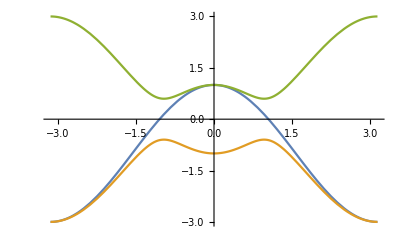

```mathematica
Plot[{-(M0+2*M1(1-Cos[Subscript[k, x]])),-Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]]))^2+2*A1^2*Sin[Subscript[k, x]]^2],Sqrt[(M0+2*M1(1-Cos[Subscript[k, x]]))^2+2*A1^2*Sin[Subscript[k, x]]^2]},{Subscript[k, x],-Pi,Pi}]
```

```mathematica
Integrate[Sqrt[a^2+b^2*Sin[θ]^2+c^2*Cos[θ]^2],{θ,0,2*Pi}]
```

ConditionalExpression[4 √(a^2+c^2) EllipticE[(-b^2+c^2)/(a^2+c^2)], ]

```mathematica
Solve[0.9*Sqrt[2]*0.5*x/Sqrt[(-1+x^2+Sqrt[(-1+x^2)^2+2*0.5^2*x^2])^2+2*0.5^2*x^2]==Sqrt[3]/2,x]
```

{{x→0.578527}}

```mathematica
D[Sqrt[(-1+x^2)^2+2*0.5^2*x^2],x]
```

(1. x+4 x (-1+x^2))/(2 √(0.5 x^2+(-1+x^2)^2))

```mathematica
Solve[D[Sqrt[(-1+x^2)^2+2*0.5^2*x^2],x]==0]
```

```mathematica
{{x->-0.8660254037844386},{x->0.},{x->0.8660254037844386}}
Subscript[x, 1]=0.8660254037844386
```

{{x→-0.866025},{x→0.},{x→0.866025}}

0.866025

```mathematica
Sqrt[(-1+Subscript[x, 1]^2)^2+2*0.5^2*Subscript[x, 1]^2]
```

0.661438

```mathematica
Solve[-1+x^2==0.6614378277661477,x]
```

{{x→-1.28897},{x→1.28897}}

```mathematica
Subscript[x, 2]=1.2889677372867592
```

1.28897

```mathematica
-1.2889677372867592
```

-1.28897

```mathematica
Subscript[x, 6]=(Subscript[x, 1]+Subscript[x, 2])/2 
Subscript[x, 1]/Subscript[x, 6]
```

1.0775

0.803738

```mathematica
Solve[Sqrt[(-1+x^2)^2+2*0.5^2*x^2]==1,x]
```

{{x→-1.22474},{x→0.},{x→1.22474}}

```mathematica
Subscript[x, 3]=1.224744871391589
```

1.22474

```mathematica
Subscript[x, 4]=Sqrt[2]
```

√2

```mathematica
Subscript[x, 5]=2*Subscript[x, 3]/(Subscript[x, 3]+Subscript[x, 4])
```

0.928203

```mathematica
(Subscript[x, 5]+Subscript[x, 6])/2
```

0.865971

```mathematica
Solve[0.928*Sqrt[2]*0.5*x/Sqrt[(-1+x^2-Sqrt[(-1+x^2)^2+2*0.5^2*x^2])^2+2*0.5^2*x^2]==Sqrt[3]/2,x]
```

{{x→1.46481}}

```mathematica
Plot[{Sqrt[(-1+x^2)^2+0.5^2*x^2],-Sqrt[(-1+x^2)^2+0.5^2*x^2],0.5,-0.5},{x,-1.3,1.3},PlotStyle->{Thickl,RGBColor[0.28076729600000006, 0.523063248, 0.7793954160000001],RGBColor[0.866654104, 0.20372769600000007, 0.14483014400000002],RGBColor[0.866654104, 0.20372769600000007, 0.14483014400000002]},PlotStyle->{Thick,Thick,Thickness[1],Thickness[2]}]
```

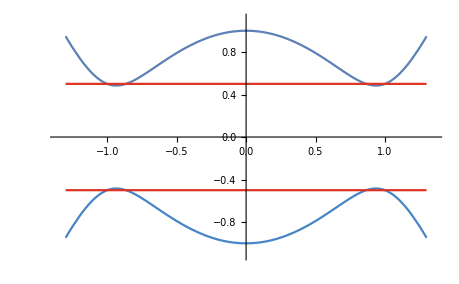

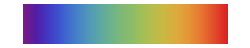

```mathematica
ColorData["Rainbow","Panel"]
```

```mathematica
RGBColor[0.866654104, 0.20372769600000007, 0.14483014400000002]RGBColor[0.294139088, 0.556297344, 0.7582734480000001]
```